```mathematica
(* Figure out the rotation that puts the signal and idler into the pump coordinates. Here θ is the opening angle and ϕ is the azimuthal angle.
*)
RotX:= {{1, 0, 0},{0, Cos[θ],Sin[θ]}, {0, -Sin[θ], Cos[θ]}}
RotZ:={{ Cos[ϕ],Sin[ϕ], 0}, {-Sin[ϕ], Cos[ϕ], 0}, {0,0,1}}

RotTrans=RotZ . RotX
```

{{Cos[ϕ],Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ]},{-Sin[ϕ],Cos[θ] Cos[ϕ],Cos[ϕ] Sin[θ]},{0,-Sin[θ],Cos[θ]}}

```mathematica
(* We can use the fact that Subscript[ϕ, i]= Subscript[ϕ, s]+π to simplify things somewhat. Here are the coordinate transformations for the signal and idler. Eventually, these terms will include the walkoff angles for the signal, idler, and pump. For now, this is more tractable.*)
Subscript[x, s] := Cos[Subscript[ϕ, s]]*x + Cos[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*y + Sin[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*z
Subscript[y, s]:= -Sin[Subscript[ϕ, s]]*x + Cos[Subscript[θ, s]]*Cos[Subscript[ϕ, s]]*y + Sin[Subscript[θ, s]]*Cos[Subscript[ϕ, s]]*z
Subscript[z, s]:= -Sin[Subscript[θ, s]]*y + Cos[Subscript[θ, s]]*z

Subscript[x, i] := -Cos[Subscript[ϕ, s]]*x - Cos[Subscript[θ, i]]*Sin[Subscript[ϕ, s]]*y - Sin[Subscript[θ, i]]*Sin[Subscript[ϕ, s]]*z
Subscript[y, i]:= Sin[Subscript[ϕ, s]]*x - Cos[Subscript[θ, i]]*Cos[Subscript[ϕ, s]]*y - Sin[Subscript[θ, i]]*Cos[Subscript[ϕ, s]]*z
Subscript[z, i]:= -Sin[Subscript[θ, i]]*y + Cos[Subscript[θ, i]]*z

(*Here is the argument in the exponential that we will want to integrate over wrt to x, y, and z.
*)
```

```mathematica
Arg1=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, i])(Subscript[x, i]^2+Subscript[y, i]^2)-1/(2*Subscript[q, p])*(x^2+y^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)
```

-((-y Cos[θ_i] Cos[ϕ_s]-z Cos[ϕ_s] Sin[θ_i]+x Sin[ϕ_s])^2+(-x Cos[ϕ_s]-y Cos[θ_i] Sin[ϕ_s]-z Sin[θ_i] Sin[ϕ_s])^2)/(2 q_i)-(x^2+y^2)/(2 q_p)-((y Cos[θ_s] Cos[ϕ_s]+z Cos[ϕ_s] Sin[θ_s]-x Sin[ϕ_s])^2+(x Cos[ϕ_s]+y Cos[θ_s] Sin[ϕ_s]+z Sin[θ_s] Sin[ϕ_s])^2)/(2 q_s)-ⅈ (x ΔK_x+y ΔK_y+z ΔK_z)

```mathematica
CompleteSquare[f_,x_]:=Module[{a,b,c},
{c,b,a}=CoefficientList[f,x];
a(x+b/2/a)^2+Simplify[(c-b^2/4/a)]
]
```

```mathematica
(* First we complete the square wrt to x. This makes it easier to analytically carry out the integration.
*)
Arg1 = CompleteSquare[Arg1, x]
```

(-Cos[ϕ_s]^2/(2 q_i)-Sin[ϕ_s]^2/(2 q_i)-1/(2 q_p)-Cos[ϕ_s]^2/(2 q_s)-Sin[ϕ_s]^2/(2 q_s)) (x-(ⅈ ΔK_x)/(2 (-Cos[ϕ_s]^2/(2 q_i)-Sin[ϕ_s]^2/(2 q_i)-1/(2 q_p)-Cos[ϕ_s]^2/(2 q_s)-Sin[ϕ_s]^2/(2 q_s))))^2+1/4 (-(2 (y Cos[θ_i]+z Sin[θ_i])^2)/q_i-(2 q_i q_p q_s ΔK_x^2)/(q_p q_s+q_i (q_p+q_s))-(2 (y^2 q_s+q_p ((y Cos[θ_s]+z Sin[θ_s])^2+2 ⅈ q_s (y ΔK_y+z ΔK_z))))/(q_p q_s))

```mathematica
(* Now, the term in the b*(x-a)^2 term integrates to a constant*)
xconst:= √π/-(-Cos[Subscript[ϕ, s]]^2/(2 Subscript[q, i])-Sin[Subscript[ϕ, s]]^2/(2 Subscript[q, i])-1/(2 Subscript[q, p])-Cos[Subscript[ϕ, s]]^2/(2 Subscript[q, s])-Sin[Subscript[ϕ, s]]^2/(2 Subscript[q, s]))
 
(*now we can do the remaining integral wrt y and complete the square agaim*)
yArg:= 1/4 (-(2 (y Cos[Subscript[θ, i]]+z Sin[Subscript[θ, i]])^2)/Subscript[q, i]-(2 Subscript[q, i] Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/(Subscript[q, p] Subscript[q, s]+Subscript[q, i] (Subscript[q, p]+Subscript[q, s]))-(2 (y^2 Subscript[q, s]+Subscript[q, p] ((y Cos[Subscript[θ, s]]+z Sin[Subscript[θ, s]])^2+2 ⅈ Subscript[q, s] (y Subscript[ΔK, y]+z Subscript[ΔK, z]))))/(Subscript[q, p] Subscript[q, s]))
yArg2=CompleteSquare[yArg,y]
```

(-Cos[θ_i]^2/(2 q_i)-1/(2 q_p)-Cos[θ_s]^2/(2 q_s)) (y+(-(z Cos[θ_i] Sin[θ_i])/q_i-(z Cos[θ_s] Sin[θ_s])/q_s-ⅈ ΔK_y)/(2 (-Cos[θ_i]^2/(2 q_i)-1/(2 q_p)-Cos[θ_s]^2/(2 q_s))))^2+1/4 (-(2 z^2 Sin[θ_i]^2)/q_i-(2 z^2 Sin[θ_s]^2)/q_s-(2 q_i q_p q_s ΔK_x^2)/(q_p q_s+q_i (q_p+q_s))+(q_p (z Sin[2 θ_i] q_s+q_i (z Sin[2 θ_s]+2 ⅈ q_s ΔK_y))^2)/(2 q_i q_s (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))-4 ⅈ z ΔK_z)

```mathematica
(*now the constant that remains after integrating over y is:*)
yconst = Simplify[ √π/- (-Cos[Subscript[θ, i]]^2/(2 Subscript[q, i])-1/(2 Subscript[q, p])-Cos[Subscript[θ, s]]^2/(2 Subscript[q, s]))]
```

(2 √π q_i q_p q_s)/(Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s))

```mathematica
(*This leaves the remaing z integrand*)
ArgZ:=1/4 (-(2 z^2 Sin[Subscript[θ, i]]^2)/Subscript[q, i]-(2 z^2 Sin[Subscript[θ, s]]^2)/Subscript[q, s]-(2 Subscript[q, i] Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/(Subscript[q, p] Subscript[q, s]+Subscript[q, i] (Subscript[q, p]+Subscript[q, s]))+(Subscript[q, p] (z Sin[2 Subscript[θ, i]] Subscript[q, s]+Subscript[q, i] (z Sin[2 Subscript[θ, s]]+2 ⅈ Subscript[q, s] Subscript[ΔK, y]))^2)/(2 Subscript[q, i] Subscript[q, s] (Cos[Subscript[θ, i]]^2 Subscript[q, p] Subscript[q, s]+Subscript[q, i] (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s])))-4 ⅈ z Subscript[ΔK, z])

Collect[ArgZ, z]
```

1/4 z^2 (-(2 Sin[θ_i]^2)/q_i-(2 Sin[θ_s]^2)/q_s+(Sin[2 θ_i] Sin[2 θ_s] q_p)/(Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s))+(Sin[2 θ_s]^2 q_i q_p)/(2 q_s (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))+(Sin[2 θ_i]^2 q_p q_s)/(2 q_i (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s))))+1/4 (-(2 q_i q_p q_s ΔK_x^2)/(q_p q_s+q_i (q_p+q_s))-(2 q_i q_p q_s ΔK_y^2)/(Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))+1/4 z ((2 ⅈ Sin[2 θ_s] q_i q_p ΔK_y)/(Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s))+(2 ⅈ Sin[2 θ_i] q_p q_s ΔK_y)/(Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s))-4 ⅈ ΔK_z)

```mathematica
(* Introduce the assumption that the Rayleigh range is much longer than the crystal length and the waist can be treated as a constant. This dramatically simplifies things.
*)
rules2 :={Subscript[q, p] -> Subscript[W, p]^2 , Subscript[q, s] -> Subscript[W, s]^2 , Subscript[q, i] -> Subscript[W, i]^2 } 
xconst = xconst //. rules2;
yconst = yconst //. rules2;
ArgZ=Collect[ArgZ //.rules2,z]
```

1/4 z^2 (-(2 Sin[θ_i]^2)/W_i^2-(2 Sin[θ_s]^2)/W_s^2+(Sin[2 θ_i] Sin[2 θ_s] W_p^2)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))+(Sin[2 θ_s]^2 W_i^2 W_p^2)/(2 W_s^2 (Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))+(Sin[2 θ_i]^2 W_p^2 W_s^2)/(2 W_i^2 (Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))))+1/4 (-(2 W_i^2 W_p^2 W_s^2 ΔK_x^2)/(W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2))-(2 W_i^2 W_p^2 W_s^2 ΔK_y^2)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))+1/4 z ((2 ⅈ Sin[2 θ_s] W_i^2 W_p^2 ΔK_y)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))+(2 ⅈ Sin[2 θ_i] W_p^2 W_s^2 ΔK_y)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))-4 ⅈ ΔK_z)

```mathematica
(* The integral has a familar form. Let's see if Mathematica can do the integration straight up. Otherwise, compare it to a known solution
*)
IntZ:=Simplify[Exp[ArgZ] *yconst*xconst//. rules2]
Assuming[Subscript[W, i]>0  &&  Subscript[W, s]>0  && Subscript[W, p]>0 && Subscript[ΔK, x]>0 && Subscript[ΔK, y]>0 && Subscript[ΔK, z]>0  && Subscript[θ, i]>0 && Subscript[θ, s]>0,   Integrate[IntZ, {z,0,L}]]
```

∫_0^L (4 ⅇ^(1/2 (-(z^2 (Sin[θ_s]^2 W_i^2+Sin[θ_i-θ_s]^2 W_p^2+Sin[θ_i]^2 W_s^2))/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))-(W_i^2 W_p^2 W_s^2 ΔK_x^2)/(W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2))-(W_i^2 W_p^2 W_s^2 ΔK_y^2)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))+(ⅈ z (W_p^2 W_s^2 (Sin[2 θ_i] ΔK_y-2 Cos[θ_i]^2 ΔK_z)+W_i^2 (-2 W_s^2 ΔK_z+W_p^2 (Sin[2 θ_s] ΔK_y-2 Cos[θ_s]^2 ΔK_z))))/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))) π W_i^4 W_p^4 W_s^4)/((W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2)) (Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))ⅆz

```mathematica
(* Mathematica can't integrate this. Look at coefficients for the integral to get it in the right form*)
AA:= -1/4  (-(2 Sin[Subscript[θ, i]]^2)/Subscript[W, i]^2-(2 Sin[Subscript[θ, s]]^2)/Subscript[W, s]^2+(Sin[2 Subscript[θ, i]] Sin[2 Subscript[θ, s]] Subscript[W, p]^2)/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))+(Sin[2 Subscript[θ, s]]^2 Subscript[W, i]^2 Subscript[W, p]^2)/(2 Subscript[W, s]^2 (Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2)))+(Sin[2 Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2)/(2 Subscript[W, i]^2 (Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))))
BB:=-1/4  ((2  Sin[2 Subscript[θ, s]] Subscript[W, i]^2 Subscript[W, p]^2 Subscript[ΔK, y])/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))+(2  Sin[2 Subscript[θ, i]] Subscript[W, p]^2 Subscript[W, s]^2 Subscript[ΔK, y])/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))-4  Subscript[ΔK, z])
CC:= -1/4 (-(2 Subscript[W, i]^2 Subscript[W, p]^2 Subscript[W, s]^2 Subscript[ΔK, x]^2)/(Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Subscript[W, p]^2+Subscript[W, s]^2))-(2 Subscript[W, i]^2 Subscript[W, p]^2 Subscript[W, s]^2 Subscript[ΔK, y]^2)/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2)))

IZ:=- AA*z^2 -ⅈ*BB*z - CC
```

```mathematica
(*This leaves us with real coefficients for z^2 and imaginary coefficents for z. Now, this integral leads to error functions. Instead, look at Taylor expanding what is in the integrand and then carry out the integral.*)

IntResult=Assuming[R>-inf && S>-inf && T>-inf , Integrate[Series[Exp[-z^2 *(R ) -z *(ⅈ*S) - T],{z,0,5}],{z,0,L}]]
```

ⅇ^-T L-1/2 ⅈ ⅇ^-T S L^2-1/6 (ⅇ^-T (2 R+S^2)) L^3+1/24 ⅈ ⅇ^-T S (6 R+S^2) L^4+1/120 ⅇ^-T (12 R^2+12 R S^2+S^4) L^5-1/720 ⅈ ⅇ^-T S (60 R^2+20 R S^2+S^4) L^6+O[L]^7

```mathematica
(* So, by doing the series expansion to the 5th order, we can easily find the integral. Here R = AA, S = BB, and T= CC. This isn't terrible as AA, BB, and CC are just constants and can be individually evaluated easily.  At the bottom of this workbook I test how valid this approximation is. As long as L*Sqrt[R] <1 the error should be less than ~1%. As L*Sqrt[R] <<1, the approx is very good.
*)
(*Simplify[IntResult //.{R -> AA, S -> BB, T -> CC}]*)

(*If we assume that Ws = Wi, then we get even further simplification. Don't think I want to do this in the final program.*)
AAsame = Simplify[AA //. {Subscript[W, i] -> Subscript[W, s]}]
BBsame = Simplify[BB //. {Subscript[W, i] -> Subscript[W, s]}]
CCsame = Simplify[CC //. {Subscript[W, i] -> Subscript[W, s]}]
```

-(-2 Sin[θ_i-θ_s]^2 W_p^2+(-2+Cos[2 θ_i]+Cos[2 θ_s]) W_s^2)/(4 W_s^2 ((Cos[θ_i]^2+Cos[θ_s]^2) W_p^2+W_s^2))

(2 W_s^2 ΔK_z+W_p^2 (-(Sin[2 θ_i]+Sin[2 θ_s]) ΔK_y+(2+Cos[2 θ_i]+Cos[2 θ_s]) ΔK_z))/(2 ((Cos[θ_i]^2+Cos[θ_s]^2) W_p^2+W_s^2))

(W_p^2 W_s^2 (W_s^2 (ΔK_x^2+ΔK_y^2)+W_p^2 ((Cos[θ_i]^2+Cos[θ_s]^2) ΔK_x^2+2 ΔK_y^2)))/(2 (2 W_p^2+W_s^2) ((Cos[θ_i]^2+Cos[θ_s]^2) W_p^2+W_s^2))

```mathematica
(*OK, now what if we substitute in the values for q_p and q_s. Need to start over!

Arg2:=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, i])(Subscript[x, i]^2+Subscript[y, i]^2)-1/(2*Subscript[q, p])*(x^2+y^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)

rules1 :={Subscript[q, p] -> Subscript[W, p]^2 + 2*ⅈ*z/Subscript[k, p], Subscript[q, s] -> Subscript[W, s]^2 - 2*ⅈ*Subscript[z, s]/Subscript[k, s], Subscript[q, i] -> Subscript[W, i]^2 - 2*ⅈ*Subscript[z, i]/Subscript[k, i], Subscript[z, s] -> -Sin[Subscript[θ, s]]*y + Cos[Subscript[θ, s]]*z, Subscript[z, i] -> -Sin[Subscript[θ, i]]*y + Cos[Subscript[θ, i]]*z} 


Arg2 =Simplify[ Arg2 //. rules1] *)

(*Turns out this is way to hard. Going to ignore it*)
```

```mathematica
(* OK, so now I need to find the collection rate into just one of the fibers. This is done by dropping the Gaussian integral of the idler photon, then repeating the same procedure.
*)

ArgSingles:=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, p])*(x^2+y^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)
ArgS = CompleteSquare[ArgSingles, x]
```

(-1/(2 q_p)-Cos[ϕ_s]^2/(2 q_s)-Sin[ϕ_s]^2/(2 q_s)) (x-(ⅈ ΔK_x)/(2 (-1/(2 q_p)-Cos[ϕ_s]^2/(2 q_s)-Sin[ϕ_s]^2/(2 q_s))))^2-(2 y^2 q_s^2+2 q_p^2 ((y Cos[θ_s]+z Sin[θ_s])^2+q_s^2 ΔK_x^2+2 ⅈ q_s (y ΔK_y+z ΔK_z))+q_p q_s (3 y^2+z^2+(y^2-z^2) Cos[2 θ_s]+2 y z Sin[2 θ_s]+4 ⅈ q_s (y ΔK_y+z ΔK_z)))/(4 q_p q_s (q_p+q_s))

```mathematica
xconsts := Simplify[(√π)/(√-(-1/(2 Subscript[q, p])-Cos[Subscript[ϕ, s]]^2/(2 Subscript[q, s])-Sin[Subscript[ϕ, s]]^2/(2 Subscript[q, s])))//. rules2]
yints := -(2 y^2 Subscript[q, s]^2+2 Subscript[q, p]^2 ((y Cos[Subscript[θ, s]]+z Sin[Subscript[θ, s]])^2+Subscript[q, s]^2 Subscript[ΔK, x]^2+2 ⅈ Subscript[q, s] (y Subscript[ΔK, y]+z Subscript[ΔK, z]))+Subscript[q, p] Subscript[q, s] (3 y^2+z^2+(y^2-z^2) Cos[2 Subscript[θ, s]]+2 y z Sin[2 Subscript[θ, s]]+4 ⅈ Subscript[q, s] (y Subscript[ΔK, y]+z Subscript[ΔK, z])))/(4 Subscript[q, p] Subscript[q, s] (Subscript[q, p]+Subscript[q, s]))
yints = CompleteSquare[yints, y]
```

(-3/(4 (q_p+q_s))-Cos[2 θ_s]/(4 (q_p+q_s))-(Cos[θ_s]^2 q_p)/(2 q_s (q_p+q_s))-q_s/(2 q_p (q_p+q_s))) (y+(-(z Sin[2 θ_s])/(2 (q_p+q_s))-(z Cos[θ_s] Sin[θ_s] q_p)/(q_s (q_p+q_s))-(ⅈ q_p ΔK_y)/(q_p+q_s)-(ⅈ q_s ΔK_y)/(q_p+q_s))/(2 (-3/(4 (q_p+q_s))-Cos[2 θ_s]/(4 (q_p+q_s))-(Cos[θ_s]^2 q_p)/(2 q_s (q_p+q_s))-q_s/(2 q_p (q_p+q_s)))))^2-(z q_s (z Sin[θ_s]^2+2 ⅈ q_s ΔK_z)+q_p^2 (q_s (Cos[θ_s]^2 ΔK_x^2+ΔK_y^2)-ⅈ z (Sin[2 θ_s] ΔK_y-2 Cos[θ_s]^2 ΔK_z))+q_p (z^2 Sin[θ_s]^2+q_s^2 (ΔK_x^2+ΔK_y^2)-ⅈ z q_s (Sin[2 θ_s] ΔK_y-(3+Cos[2 θ_s]) ΔK_z)))/(2 (q_p+q_s) (Cos[θ_s]^2 q_p+q_s))

```mathematica
(* This leaves us with the y constant and the z integrand
*)

yconsts := Simplify[(√π)/(√-(-3/(4 (Subscript[q, p]+Subscript[q, s]))-Cos[2 Subscript[θ, s]]/(4 (Subscript[q, p]+Subscript[q, s]))-(Cos[Subscript[θ, s]]^2 Subscript[q, p])/(2 Subscript[q, s] (Subscript[q, p]+Subscript[q, s]))-Subscript[q, s]/(2 Subscript[q, p] (Subscript[q, p]+Subscript[q, s])))) //. rules2]
zints :=-(z Subscript[q, s] (z Sin[Subscript[θ, s]]^2+2 ⅈ Subscript[q, s] Subscript[ΔK, z])+Subscript[q, p]^2 (Subscript[q, s] (Cos[Subscript[θ, s]]^2 Subscript[ΔK, x]^2+Subscript[ΔK, y]^2)-ⅈ z (Sin[2 Subscript[θ, s]] Subscript[ΔK, y]-2 Cos[Subscript[θ, s]]^2 Subscript[ΔK, z]))+Subscript[q, p] (z^2 Sin[Subscript[θ, s]]^2+Subscript[q, s]^2 (Subscript[ΔK, x]^2+Subscript[ΔK, y]^2)-ⅈ z Subscript[q, s] (Sin[2 Subscript[θ, s]] Subscript[ΔK, y]-(3+Cos[2 Subscript[θ, s]]) Subscript[ΔK, z])))/(2 (Subscript[q, p]+Subscript[q, s]) (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]))
(*Now make the subsitution where we assume that the waist is constant in the crystal
*)

zints = Collect[zints //. rules2, z]
```

-(z^2 (Sin[θ_s]^2 W_p^2+Sin[θ_s]^2 W_s^2))/(2 (W_p^2+W_s^2) (Cos[θ_s]^2 W_p^2+W_s^2))-(W_p^2 W_s^4 (ΔK_x^2+ΔK_y^2)+W_p^4 W_s^2 (Cos[θ_s]^2 ΔK_x^2+ΔK_y^2))/(2 (W_p^2+W_s^2) (Cos[θ_s]^2 W_p^2+W_s^2))-(z (2 ⅈ W_s^4 ΔK_z-ⅈ W_p^4 (Sin[2 θ_s] ΔK_y-2 Cos[θ_s]^2 ΔK_z)-ⅈ W_p^2 W_s^2 (Sin[2 θ_s] ΔK_y-(3+Cos[2 θ_s]) ΔK_z)))/(2 (W_p^2+W_s^2) (Cos[θ_s]^2 W_p^2+W_s^2))

```mathematica
(* Same form of the integral before. Now we have:
*)
Subscript[AA, singles]:=Simplify[ (Sin[Subscript[θ, s]]^2 Subscript[W, p]^2+Sin[Subscript[θ, s]]^2 Subscript[W, s]^2)/(2 (Subscript[W, p]^2+Subscript[W, s]^2) (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))]
Subscript[BB, singles]:= Simplify[(2  Subscript[W, s]^4 Subscript[ΔK, z]- Subscript[W, p]^4 (Sin[2 Subscript[θ, s]] Subscript[ΔK, y]-2 Cos[Subscript[θ, s]]^2 Subscript[ΔK, z])- Subscript[W, p]^2 Subscript[W, s]^2 (Sin[2 Subscript[θ, s]] Subscript[ΔK, y]-(3+Cos[2 Subscript[θ, s]]) Subscript[ΔK, z]))/(2 (Subscript[W, p]^2+Subscript[W, s]^2) (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))]
Subscript[CC, singles]:=Simplify[ (Subscript[W, p]^2 Subscript[W, s]^4 (Subscript[ΔK, x]^2+Subscript[ΔK, y]^2)+Subscript[W, p]^4 Subscript[W, s]^2 (Cos[Subscript[θ, s]]^2 Subscript[ΔK, x]^2+Subscript[ΔK, y]^2))/(2 (Subscript[W, p]^2+Subscript[W, s]^2) (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))]
```

```mathematica
(* We can use the same series expansion for the integral, now with different coefficients.

First, let's look at the prefactors. The relationship for efficiency is E = Subscript[P, coinc] / Subscript[P, singles]
*)

prefactor= Simplify[(xconst*yconst)^2/(xconsts*yconsts)^2]
```

(4 W_i^8 W_p^4 W_s^4 (W_p^2+W_s^2) (Cos[θ_s]^2 W_p^2+W_s^2))/((W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2))^2 (Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))^2)

```mathematica
(* That worked out nicer than expected! Now let's try the ratio of the series expansion of the two integrals.
*)

Subscript[P, coinc] := IntResult^2 //. {R -> AA, S -> BB, T -> CC}
Subscript[P, singles]:= IntResult^2 //. {R -> Subscript[AA, singles], S -> Subscript[BB, singles], T -> Subscript[CC, singles]}
(*Eff := Subscript[P, coinc]/Subscript[P, singles]*)
(* This gets ugly in a hurry. abort!*)
```

```mathematica
(* Let's test how accurate the order of the expansions is of the integral *)

inttest:= N*Exp[-z^2 *(R ) -z *(ⅈ*S) - T]

IntResultExact = Assuming[R>-inf && S>-inf && T>-inf , Integrate[inttest,{z,0,L}]]
(*IntResult5E := Normal[Series[IntResultExact,{S,0,10}] //. { Erf[L √R] -> Series[ Erf[L √R], {L,0,10}]}]*)
(*IntResult15 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[Exp[-z^2 *(R ) -z *(ⅈ*S) - T],{z,0,15}]],{z,0,L}]]*)
IntResult5 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,5}]],{z,0,L}]]
IntResult3 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,3}]],{z,0,L}]]
IntResult1 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,1}]],{z,0,L}]]
IntResult7 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,7}]],{z,0,L}]]
IntResult9 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,9}]],{z,0,L}]]
```

(ⅇ^(-S^2/(4 R)-T) N √π (Erf[(2 L R+ⅈ S)/(2 √R)]-ⅈ Erfi[S/(2 √R)]))/(2 √R)

```mathematica
(* Consider a collinear, perfectly phasematched system with the signal and pump waists as 100 microns*)
rulessamle :={Subscript[θ, s] ->10*π/180, Subscript[W, s]  -> .0001,  Subscript[W, p]  -> .0001, Subscript[ΔK, z] ->0,  Subscript[ΔK, x] -> 0,  Subscript[ΔK, y] -> 0}

AAtest := Subscript[AA, singles] //.rulessamle
BBtest := Subscript[BB, singles] //.rulessamle
CCtest := Subscript[CC, singles] //.rulessamle
 
(* Crystal length in meters*)
Lxtal := 0.001

(* isvalidapprox should be < 1 to keep the errors in check with a 5th order series expansion*)
isvalidapprox = Lxtal *Sqrt[AAtest]
NN := xconsts*yconsts //.rulessamle

rulessub := {R ->AAtest, S -> BBtest, T -> CCtest, L -> Lxtal, N -> 1}
InE:= IntResultExact //. rulessub

diff1=(IntResult1-InE)/InE //.rulessub
diff3= (IntResult3-InE) /InE //. rulessub
diff5= (IntResult5-InE) /InE//. rulessub
diff7= (IntResult7-InE) /InE//. rulessub
diff9= (IntResult9-InE) /InE//. rulessub


(*diff7= (IntResult7-IntResult15) /IntResult15/L //. {R ->AAtest, S -> BBtest, T -> CCtest, L -> 0.001}
diff9= (IntResult9-IntResult15) /IntResult15/L //. {R ->AAtest, S -> BBtest, T -> CCtest, L -> 0.001}*)
```

0.874861

0.259148+0. ⅈ

-0.0620948+0. ⅈ

0.0116673+0. ⅈ

-0.00177462+0. ⅈ

0.000225867+0. ⅈ

(2 √R (1/720 (720-240 R+72 R^2)-(√π Erf[√R])/(2 √R)))/(√π Erf[√R])

{0.0024135,0.0195598,0.0668348,0.160298,0.316604,0.552936,0.886938,1.33665,1.92043,2.65692}

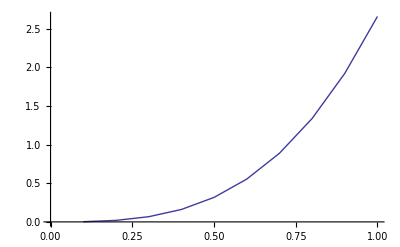

```mathematica
(* Now let's try to plot the error for 5th order expansion as a function of L*R. When there is perfect phasematching, then S and T go to 0. I am also setting L=1 to get a feel for how things scale. It should really be L*sqrt(R) that I investigate. *)
rulesplot :={ S -> 0, T -> 0,L->1,  N -> 1}
IE:=IntResultExact //.rulesplot
diff5plot = (IntResult5-IE)/IE //.rulesplot


(*data = Table[Abs[diff3plot*100], {R,.1, 1, .3}, {L,1, 2,.5}]
ListDensityPlot[data](*,  DataRange->{.1,1}]*)*)

data = Table[Abs[diff5plot*100], {R,.1, 1, .1}]
ListLinePlot[data, DataRange->{.1,1}]
(*Plot[Abs[diff3plot*100], {R, .1, 2}]*)
```

```mathematica
(* So it looks like the 5th order expansion is fine as long as L*R^0.5 << 1. Is there a better way to expand this without needing to go to a ton of terms? I tried it with the third order expansion and 9th order expansion. 
*)
```